```mathematica
Import["../libs/QuantumDavid.m"]
```

```mathematica
x=Import["trazas.txt","Table"]//ToExpression;
```

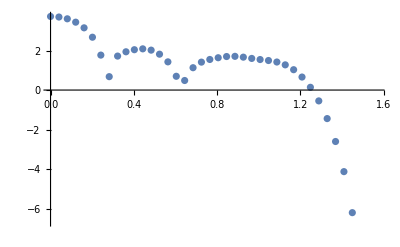

```mathematica
ListPlot[Table[{linearmesh[0,Pi/2,40][[i]],Log[10,Abs[x[[5]][[i]]]^2]},{i,1,40}]]
```